```mathematica
RBONDI=100.;
γ=.5(4/3+5/3);
Be=(5-3γ)/(4(γ-1)RBONDI);
RMAX=1000000;
ρout=10^-26;
vout=-10^-12;
```

```mathematica
cs2[r_,v_]:=(γ-1)(Be+1/r-1/2 v^2)
```

```mathematica
eqdv=D[v[r],r]==v[r]/(v[r]^2-cs2[r,v[r]])(2/r cs2[r,v[r]]-1/r^2)
```

v'[r]==(v[r] (-1/r^2+(1. (0.0025+1/r-v[r]^2/2))/r))/(v[r]^2-0.5 (0.0025+1/r-v[r]^2/2))

```mathematica
sol1=NDSolve[{eqdv,v[RMAX]==vout},v,{r,RMAX,2}]
```

{{v→InterpolatingFunction[{{2.,1.×10^6}},<>]}}

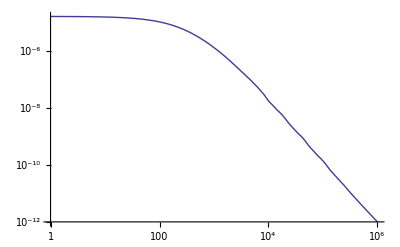

```mathematica
LogLogPlot[-Evaluate[v[r]/.sol1],{r,RMAX,1},PlotRange->All]
```

```mathematica
Clear[v]
```